# Advent of Code 2023

## Day 3

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/rlupi/src/aoc2023/3

```mathematica
testInput=StringSplit["467..114..
...*......
..35..633.
......#...
617*......
.....+.58.
..592.....
......755.
...$.*....
.664.598..", EndOfLine];
```

```mathematica
input=Import["input.txt","Lines"];
```

```mathematica
Length[input]
```

140

I will use  unevaluated forms to mark digits in the input data. So, let’s define custom formatting to make the display less cluttered:

```mathematica
maybe /: MakeBoxes[maybe[n_], StandardForm]:=FrameBox@StyleBox[MakeBoxes[n,StandardForm], FontColor->Gray, FontWeight->Bold];
digit /: MakeBoxes[digit[n_], StandardForm]:=FrameBox@StyleBox[MakeBoxes[n,StandardForm],FontColor->Red, FontWeight->Bold];
schematic /: MakeBoxes[schematic[data_], StandardForm] :=MakeBoxes[MatrixForm[data],StandardForm ]
```

```mathematica
{digit[n],maybe[n]}
```

{n,n}

## Part 1

```mathematica
ParseSchematic[input_]:=StringCases[input,
{n:DigitCharacter:>maybe[Interpreter[Integer][n]],
p:PunctuationCharacter:>p
}]//schematic;
testSchematic=ParseSchematic[testInput]
```

(4 | 6 | 7 | . | . | 1 | 1 | 4 | . | .
. | . | . | * | . | . | . | . | . | .
. | . | 3 | 5 | . | . | 6 | 3 | 3 | .
. | . | . | . | . | . | # | . | . | .
6 | 1 | 7 | * | . | . | . | . | . | .
. | . | . | . | . | + | . | 5 | 8 | .
. | . | 5 | 9 | 2 | . | . | . | . | .
. | . | . | . | . | . | 7 | 5 | 5 | .
. | . | . | $ | . | * | . | . | . | .
. | 6 | 6 | 4 | . | 5 | 9 | 8 | . | .)

This day was harder than I expected. I went off-track trying to use CellularAutomata[], but it’s too complicated. This way is much simpler...

```mathematica
ArraySweep[f_][a_]:=ArrayFilter[f[#[[2,2]],DeleteCases[ArrayRules[#],{2,2}->_]]&,a,1,Padding->"."];
```

```mathematica
MarkDigits[schematic[sc_]]:=Module[{mark},
mark[maybe[d_], neighbours_/;Count[neighbours,{_,_}->c_String/;c!="."]>0]:=digit[d];
mark[x_,_]:=x;
ArraySweep[mark][sc]//schematic
];
```

```mathematica
MarkDigits[testSchematic]
```

(4 | 6 | 7 | . | . | 1 | 1 | 4 | . | .
. | . | . | * | . | . | . | . | . | .
. | . | 3 | 5 | . | . | 6 | 3 | 3 | .
. | . | . | . | . | . | # | . | . | .
6 | 1 | 7 | * | . | . | . | . | . | .
. | . | . | . | . | + | . | 5 | 8 | .
. | . | 5 | 9 | 2 | . | . | . | . | .
. | . | . | . | . | . | 7 | 5 | 5 | .
. | . | . | $ | . | * | . | . | . | .
. | 6 | 6 | 4 | . | 5 | 9 | 8 | . | .)

```mathematica
ExpandDigits[schematic[sc_]]:=Module[{expand},
expand[maybe[d_],neighbours_/;Count[neighbours,{_,_}->digit[_]]>0]:=digit[d];
expand[x_,_]:=x;
FixedPoint[ArraySweep[expand],sc]//schematic
];
MarkDigits[testSchematic]//ExpandDigits
```

(4 | 6 | 7 | . | . | 1 | 1 | 4 | . | .
. | . | . | * | . | . | . | . | . | .
. | . | 3 | 5 | . | . | 6 | 3 | 3 | .
. | . | . | . | . | . | # | . | . | .
6 | 1 | 7 | * | . | . | . | . | . | .
. | . | . | . | . | + | . | 5 | 8 | .
. | . | 5 | 9 | 2 | . | . | . | . | .
. | . | . | . | . | . | 7 | 5 | 5 | .
. | . | . | $ | . | * | . | . | . | .
. | 6 | 6 | 4 | . | 5 | 9 | 8 | . | .)

```mathematica
ExtractNumbers[schematic[m_]]:=Block[{numbers},
numbers=Map[SequenceCases[#,{digit[_]..}]&,m];
numbers=numbers/.{digit[d_]:>d,{}->Nothing};
Apply[FromDigits[{##}]&,numbers,{2}]//Flatten
]
MarkDigits[testSchematic]//ExpandDigits//ExtractNumbers
```

{467,35,633,617,592,755,664,598}

```mathematica
MarkDigits[testSchematic]//ExpandDigits//ExtractNumbers//Total
```

4361

Ok, let’s see it on real data:

```mathematica
ParseSchematic[input]//MarkDigits//ExpandDigits//ExtractNumbers//Total
```

540212

## Part 2

```mathematica
part/: MakeBoxes[part[unique_,n_], StandardForm]:=UnderscriptBox[
FrameBox@StyleBox[MakeBoxes[n,StandardForm], FontWeight->Bold],MakeBoxes[unique,StandardForm]];
sym/:MakeBoxes[sym[unique_,class_], StandardForm]:=UnderscriptBox[MakeBoxes[class,StandardForm],MakeBoxes[unique, StandardForm]];
{part[Unique[],345],sym[Unique[],"*"]}
```

{345_($11),*_($12)}

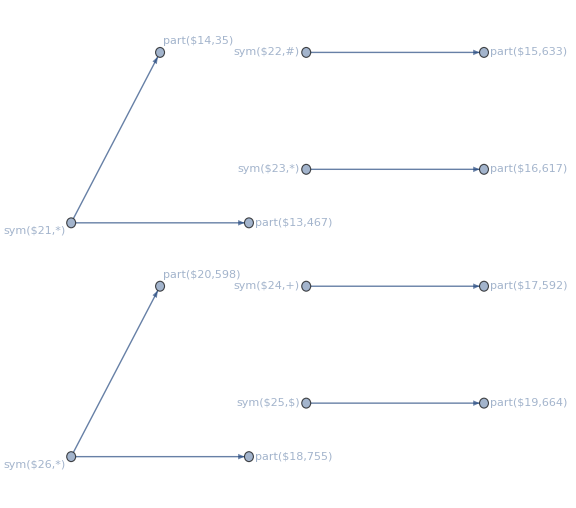

```mathematica
EngineGraph[schematic[sc_]]:=Block[{m,numbers,parts, connect,g},
m=schematic[sc]//MarkDigits//ExpandDigits //First(* First just to strip schematic *);
parts=Map[SequenceReplace[#,p:{digit[_]..}:>
Module[{u=Unique[]},Splice@Table[part[u,FromDigits@Apply[Identity,p,{1}]],Length[p]]]]&,m];
parts = parts/.{maybe[_]->".",
"."->".", (* this identity rule is needed so the next one won't apply to "." *)
c_String:>sym[Unique[],c]};
Attributes[connect]={Listable};
connect[_,{_,_}->"."]:=Nothing;
connect[".",_]:=Nothing;
connect[p_,_]:=Nothing;
connect[s_sym,{_,_}->p_part]:=s->p;
g=ArraySweep[connect][parts]//Flatten//DeleteDuplicates;
Graph[g,GraphLayout->"PlanarEmbedding",ImageSize->Large]
];
testEngine=Graph[EngineGraph[testSchematic],VertexLabels->"Name"]
```

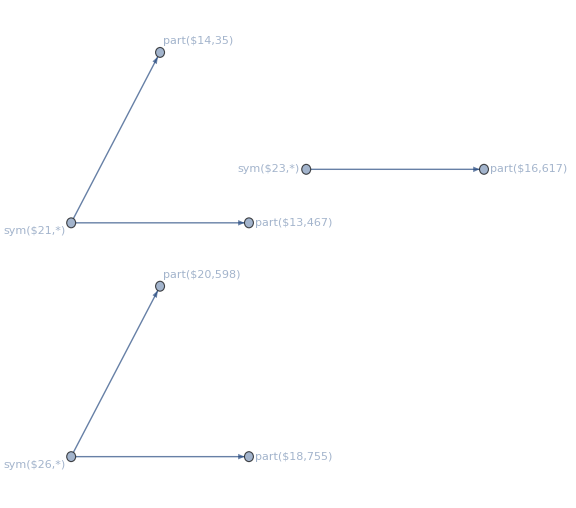

```mathematica
NeighborhoodGraph[testEngine,sym[_,"*"],VertexLabels->"Name"]
```

```mathematica
AdjacencyList[%]
```

{{467_($13),35_($14)},{617_($16)},{755_($18),598_($20)},{*_($21)},{*_($21)},{*_($23)},{*_($26)},{*_($26)}}

```mathematica
GearRatios[engine_]:=Cases[
NeighborhoodGraph[engine,sym[_,"*"]]//AdjacencyList,
{part[_,a_],part[_,b_]}:>a*b
];
GearRatios[testEngine]//Total
```

467835

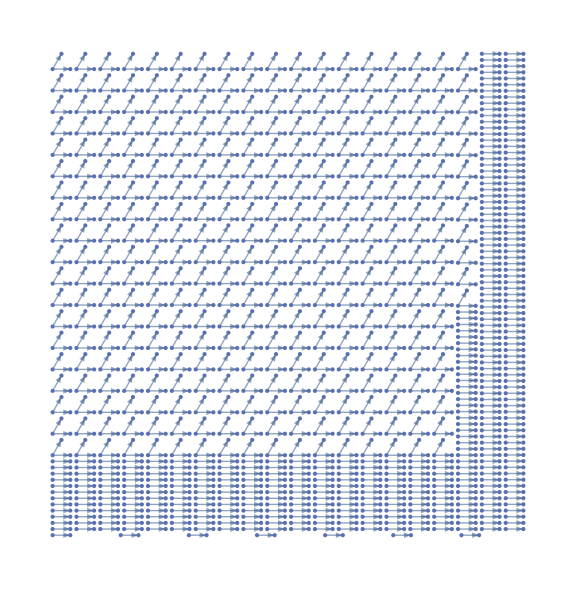

```mathematica
inputEngine=ParseSchematic[input]//EngineGraph
```

```mathematica
inputEngine//GearRatios
```

{114573,112993,153216,418264,103368,107319,379324,536635,14592,424615,507848,939378,237600,869045,141382,31520,389298,629391,46980,178920,55242,25056,635034,290580,137280,119035,358479,2205,718200,92400,202982,42828,799,23999,162710,53836,45315,246402,197308,487200,35990,986049,77748,107648,123384,344915,60588,425130,172500,356310,77280,5883,4616,324919,292400,85600,28993,2688,697375,202880,296010,542100,346500,303804,1562,462429,744753,8372,136940,58146,864,19734,108052,27474,16192,44275,226754,7294,262416,536300,687051,165483,141246,323136,22200,309072,230510,266420,607948,238720,1209,376248,65817,114450,33110,44226,301760,492156,295974,39600,186258,35400,234150,585024,194691,72412,326915,13618,511875,467138,791700,265905,165240,506880,323818,74572,131077,56376,77760,56835,335685,269726,497140,137268,117572,529549,407790,78624,46336,771524,325464,155925,31200,593732,239280,30580,263980,585984,70252,64120,695273,81534,163280,334425,268593,95484,52438,36450,136644,12495,321685,370560,348234,60138,69048,5264,194500,132132,214676,930150,62237,591414,96240,121360,23301,140990,262484,27930,203442,98154,123228,385008,635520,59109,620312,94658,157320,95106,140010,215418,779520,82181,354626,359788,7920,290523,2828,390648,75780,117199,5652,14762,533540,879522,248325,586296,344470,223539,272720,225645,155511,54510,99981,436896,44255,507952,725696,355623,893730,335465,41904,141332,105984,573678,267804,830320,37696,287280,543361,8944,211575,722638,50260,168516,835347,321763,646000,853432,78624,669390,228900,327651,20470,258390,133892,163014,368510,244800,452226,266250,553220,42616,89344,520047,86154,767457,347260,268640,557004,270720,167856,805,309650,417720,165132,315900,310415,82350,441780,366230,356265,352944,153679,879588,10114,246912,204315,90240,663060,558,66132,443700,246759,163928,161910,140608,174966,26622,189663,15072,64460,22950,145921,90168,459277,351372,22605,322328,325926,224406,86994,1282,313760,558279,273132,88995,280014,214061,22473,244278,59280,161850,35154,689724,274628,658176,94248,42529,244188,236800,131588,186214,424200,11676,206468,85436,458658,39693,818380,591364,29202,271566,32760,155574,24288,318756,12276,545616,95125,920178,604800,508980,558297,315840,859142}

```mathematica
inputEngine//GearRatios//Total
```

87605697